# Tutorial: Using the Osculating Orbital Elements Package

## Importing the Package

The package is imported using the following command. This package requires the KerrGeodesics Package, which can be found at github.com/BlackHolePerturbationToolkit/KerrGeodesics

```mathematica
<<OsculatingOrbitalElements`
```

## Schwarzschild Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements first derived in Pound and Poisson[1]. This code adopts the notation used in Warburton et al [2]. 
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum
e is the eccentricity
ξ is the phase variable, defined by ξ = χ - χ_0.
The equations are integrated w.r.t the Darwin Parameter χ.
Fr and Fϕ are contrvarient componets of the acceleration.

#### SchwarzOsculatingOrbitalElements

```mathematica
?SchwarzOsculatingOrbitalElements
```

SchwarzOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

### User Specified Model

First, we are going to define force components for use with SchwarzOsculatingOrbitalElements. These components need to be functions of p, e and ξ.

```mathematica
Fr[p_, e_, ξ_] :=-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) ;
Fϕ[p_, e_, ξ_] := -(1+e Cos[ξ])^2/(p √(-3-e^2+p));
```

Next, we specify the mass ratio along with initial conditions of the orbit.

```mathematica
η=10^-5;
p0=12;
e0=0.2;
ξ0=0.0;
```

Now we solve the osculating geodesic equations and save the result to the symbol ‘orbit’

```mathematica
orbit = SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$7648,θ→OsculatingOrbitalElements`Private`θsol$7648,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

The output is an association. You can access these functions using the following syntax:

```mathematica
orbit["r"][100]
```

12.563

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimit = orbit["t"]["Domain"][[1,2]]
```

292.966

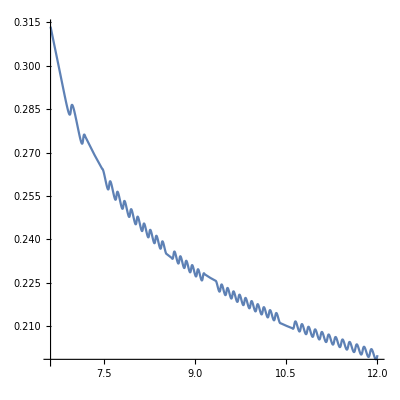

```mathematica
ParametricPlot[{orbit["p"][χ], orbit["e"][χ]}, {χ, 0, plotLimit}, AspectRatio->1]
```

```mathematica
?Disk
```

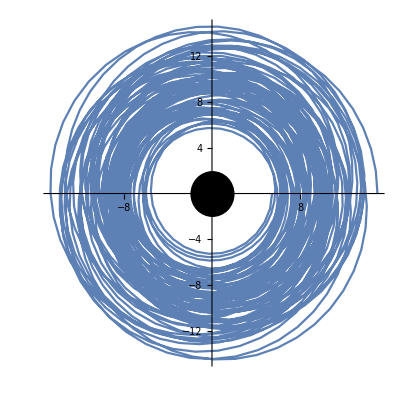

```mathematica
Show[ParametricPlot[{orbit["r"][χ]Cos[orbit["ϕ"][χ]], orbit["r"][χ]Sin[orbit["ϕ"][χ]]}, {χ, 0, plotLimit}, AspectRatio->1],{Graphics[Disk[{0,0},2]]}]
```

### Included Models

#### SchwarzGasDrag

Not specifying a Force option means that SchwarzOsculatingOrbitalElements uses the SchwarzGasDrag model.

```mathematica
?SchwarzGasDrag
```

```mathematica
SchwarzGasDrag[p, e, ξ]
```

<|Fr→-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) Sin[ξ],Fϕ→-(1+e Cos[ξ])^2/(p √(-3-e^2+p))|>

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10293,θ→OsculatingOrbitalElements`Private`θsol$10293,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

One can also specify this option explicitly.

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzGasDrag]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10843,θ→OsculatingOrbitalElements`Private`θsol$10843,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

#### SchwarzFastGSF

One can also choose to use SchwarzFastGSF model. Note that this model is valid for p <= 12 and e<= 0.2.

```mathematica
?SchwarzFastGSF
```

```mathematica
SchwarzFastGSF[p,e,ξ]
```

<|Fr→(0.-(4.42483×10^11)/p^11-(1.66118×10^14 e^2)/p^11+518+(6.07416×10^13 e^12 Cos[6 ξ])/p^2-(5.43357×10^14 e^14 Cos[6 ξ])/p^2)/p^2+(0.+(5.21159×10^17 e Sin[ξ])/p^(27/2)-1/p^1+444+(8.81955×10^16 e^12 1)/p^(9/2)-(1.02387×10^18 e^14 Sin[6 ξ])/p^(9/2))/p^(9/2),Fϕ→(0.+(2.05264×10^17)/p^1+522+1/p^1-1/p^(11/2))/p^(11/2)+(0.+450)/p^4|>
 |  |  |  |

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzFastGSF]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[{{0., 474691.}}, <>],r→OsculatingOrbitalElements`Private`rsol$12936,θ→OsculatingOrbitalElements`Private`θsol$12936,ϕ→InterpolatingFunction[{{0., 474691.}}, <>],p→InterpolatingFunction[{{0., 474691.}}, <>],e→InterpolatingFunction[{{0., 474691.}}, <>],ξ→InterpolatingFunction[{{0., 474691.}}, <>]|>

## Kerr Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements for Kerr first derived in Gair et al [3] and uses the notation given in that paper.
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum.
e is the eccentricity.
x is Cos[θinc].
En is orbital energy.
L angular momentum about the symmetry axis.
K is the modified Carter Constant defined by K = Q + (L - a (En))^2
ψr is the radial phase variable.
ψθ is the polar phase variable.
The equations are integrated w.r.t Mino time λ.
at, ar, aθ, aϕ are covariant components of the acceleration.

#### KerrOsculatingOrbitalElements

```mathematica
?KerrOsculatingOrbitalElements
```

KerrOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

### User Specified Model

First, we are going to define force components for use with KerrOsculatingOrbitalElements. These components need to be functions of En, L, K, ψr and ψθ. We’re just going to use the KerrGasDrag model for this example

```mathematica
at[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["at"];
ar[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["ar"];
aθ[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aθ"];
aϕ[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aϕ"];
```

Next, we specify the mass ratio, the spin and the initial conditions of the orbit.

```mathematica
η = 10^-5;
a0 = 0.9;
p0 = 7;
e0 = 0.5;
x0 = Cos[π/6];
ψr0 = 0;
ψθ0 =0;
```

Now we solve the osculating geodesic equations and save the result to the symbol ‘kerrOrbit’

```mathematica
<<OsculatingOrbitalElements`
```

```mathematica
kerrOrbit = KerrOsculatingOrbitalElements[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {at,ar,aθ,aϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$31840,θ→OsculatingOrbitalElements`Private`θsol$31840,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$31840,p→OsculatingOrbitalElements`Private`psol$31840,e→OsculatingOrbitalElements`Private`esol$31840,x→OsculatingOrbitalElements`Private`xsol$31840,ι→OsculatingOrbitalElements`Private`ιsol$31840,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$31840,r2→OsculatingOrbitalElements`Private`r2sol$31840,z1→OsculatingOrbitalElements`Private`zmsol$31840|>

The output is an association. You can access these functions using the following syntax:

```mathematica
kerrOrbit["r"][100]
```

3.89948

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimit = kerrOrbit["t"]["Domain"][[1,2]]
```

542.826

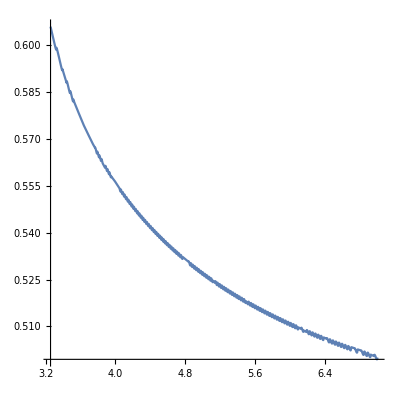

```mathematica
ParametricPlot[{kerrOrbit["p"][χ], kerrOrbit["e"][χ]}, {χ, 0, plotLimit}, AspectRatio->1]
```

### Included Models

#### KerrGasDrag

Not specifying a Force option means that KerrOsculatingOrbitalElements uses the KerrGasDrag model.

```mathematica
?KerrGasDrag
```

```mathematica
KerrGasDrag[a,En, L, K, ψr, ψθ]
```

<|at→1,ar→1,1,aϕ→-((1-((a^2 (1-En^2)+K+L^2-(1)^2-√(-4 a^2 (1-En^2) (K-(1)^2)+(1)^2)) 1^2)/(2 a^2 (1-En^2))) (((11)^2-1) (L/(1-1)-(a^2 L)/(a^2+1-1)+a En (-1+(a^2+1/1)/(a^2+1-1/1))))/((((a^2 (1-1)+6) 1^2)/(2 (1-En^2))+(4 1^2 1^2)/(1^2 1))^2)+(4 a 2 Min[1] (a L (1-1/1)+En (1)))/((Max[Re[1],Re[1]]+Min[1]) (1+1) 1^2)|>
 |  |  |  |

```mathematica
KerrOsculatingOrbitalElements[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> KerrGasDrag]
```

NDSolve::ndsz: At OsculatingOrbitalElements`Private`λ$237143 == 542.826, step size is effectively zero; singularity or stiff system suspected.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$237143,θ→OsculatingOrbitalElements`Private`θsol$237143,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$237143,p→OsculatingOrbitalElements`Private`psol$237143,e→OsculatingOrbitalElements`Private`esol$237143,x→OsculatingOrbitalElements`Private`xsol$237143,ι→OsculatingOrbitalElements`Private`ιsol$237143,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…]|>

## References

[1] arxiv.org/abs/0708.3033
[2] arxiv.org/abs/1111.6908
[3] arxiv.org/abs/1012.5111